```mathematica
minor4:=({{τ^(m-1)/Factorial[m-1], τ^m/Factorial[m], 0, 0}, {τ^(m-3)/Factorial[m-3], τ^(m-2)/Factorial[m-2], τ^(m-1)/Factorial[m-1], τ^m/Factorial[m]}, {τ^(m-5)/Factorial[m-5], τ^(m-4)/Factorial[m-4], τ^(m-3)/Factorial[m-3], τ^(m-2)/Factorial[m-2]}, {τ^(m-7)/Factorial[m-7], τ^(m-6)/Factorial[m-6], τ^(m-5)/Factorial[m-5], τ^(m-4)/Factorial[m-4]}})
FullSimplify[Det[minor4]]
```

-(16 (-3+m) (-2+m) (-9+2 m) τ^(-10+4 m))/((-1+m)^2 m^2 Gamma[-1+m]^4)

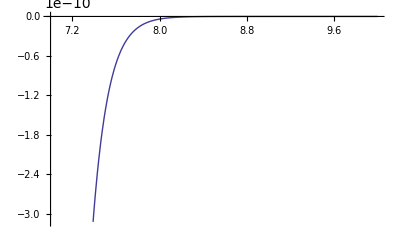

```mathematica
f[m_]:=-(16 (-3+m) (-2+m) (-9+2 m))/((-1+m)^2 m^2 Gamma[-1+m]^4)
Plot[f[m],{m,7,10}]
```

```mathematica
minor3:=({{τ^(m-1)/Factorial[m-1], τ^m/Factorial[m], 0}, {τ^(m-3)/Factorial[m-3], τ^(m-2)/Factorial[m-2], τ^(m-1)/Factorial[m-1]}, {τ^(m-5)/Factorial[m-5], τ^(m-4)/Factorial[m-4], τ^(m-3)/Factorial[m-3]}})
FullSimplify[Det[minor3]]
```

-(2 (-5+m) (-2+m) (-1+m) τ^(-6+3 m))/(Gamma[m]^2 Gamma[1+m])

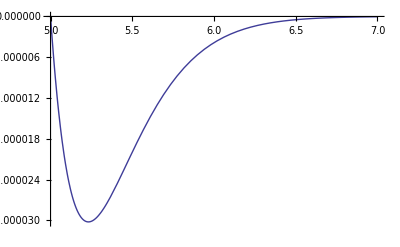

```mathematica
g[m_]:=-(2 (-5+m) (-2+m) (-1+m))/(Gamma[m]^2 Gamma[1+m])
Plot[g[m],{m,5,7}]
```

```mathematica
(32m-144)/(Factorial[m-4]*Factorial[m-2]*(Factorial[m])^2)-(16 (-3+m) (-2+m) (-9+2 m))/((-1+m)^2 m^2 (Factorial[-1+m])^4)
```

-(16 (-3+m) (-2+m) (-9+2 m))/((-1+m)^2 m^2 ((-1+m)!)^4)+(-144+32 m)/((-4+m)! (-2+m)! (m!)^2)

```mathematica
FullSimplify[(16 (-3+m) (-2+m) (-9+2 m))/((-1+m)^2 m^2 ((-1+m)!)^4)+(-144+32 m)/((-4+m)! (-2+m)! (m!)^2)]
```

(16 (-3+m) (-2+m) (-9+2 m) (2+(-2+m) m (2+(-2+m) m)))/((-1+m)^6 m^2 Gamma[-1+m]^4)